```mathematica
Quit[]
```

## Metric : modified Kerr-Newman :

#### For Figure 1 :

### Defining the metrics involved:

## Metric : modified Kerr-Newman :

```mathematica
coord={t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
n=Length[coords];
```

```mathematica
ρ[r_]= r^2+a^2(Cos[θ])^2;
```

```mathematica
Δ[r_]=r^2+a^2-2 r e^(-k/r);
```

```mathematica
tt[r_]=-{1-2r e^(-k/r)/ρ[r]};
```

```mathematica
rr[r_]=ρ[r]/Δ[r];
```

```mathematica
θθ[r_]=ρ[r];
```

```mathematica
ϕϕ[r_]=(r^2+a^2+(2a^2 r e^(-k/r)(Sin[θ])^2/ρ[r]))(Sin[θ])^2;
```

```mathematica
tϕ[r_]=-2a r e^(-k/r)(Sin[θ])^2/ρ[r];
```

```mathematica
metric={{2r e^(-k/r)/ρ[r]-1,0,0,-2a  r e^(-k/r)(Sin[θ])^2/ρ[r]},{0,ρ[r]/Δ[r],0,0},{0,0,ρ[r],0},{-2a  r e^(-k/r)(Sin[θ])^2/ρ[r],0,0,(r^2+a^2+(2a^2 r e^(-k/r)(Sin[θ])^2/ρ[r]))(Sin[θ])^2}};
```

```mathematica
metric//MatrixForm
```

(-1+(2 e^(-k/r) r)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | -(2 a e^(-k/r) r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
0 | (r^2+a^2 Cos[θ]^2)/(a^2-2 e^(-k/r) r+r^2) | 0 | 0
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
-(2 a e^(-k/r) r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | Sin[θ]^2 (a^2+r^2+(2 a^2 e^(-k/r) r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))
 |  |  |  |

```mathematica
inversemetric=Simplify[Inverse[metric]];
```

```mathematica
inversemetric//MatrixForm
```

(-(2 (a^2 e^(k/r) (a^2+r^2) Cos[θ]^2+r (e^(k/r) r (a^2+r^2)+2 a^2 Sin[θ]^2)))/((a^2 e^(k/r)+r (-2+e^(k/r) r)) (a^2+2 r^2+a^2 Cos[2 θ])) | 0 | 0 | -(4 a r)/((a^2 e^(k/r)+r (-2+e^(k/r) r)) (a^2+2 r^2+a^2 Cos[2 θ]))
0 | (a^2-2 e^(-k/r) r+r^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0
0 | 0 | 1/(r^2+a^2 Cos[θ]^2) | 0
-(4 a r)/((a^2 e^(k/r)+r (-2+e^(k/r) r)) (a^2+2 r^2+a^2 Cos[2 θ])) | 0 | 0 | (2 (r (-2+e^(k/r) r)+a^2 e^(k/r) Cos[θ]^2) Csc[θ]^2)/((a^2 e^(k/r)+r (-2+e^(k/r) r)) (a^2+2 r^2+a^2 Cos[2 θ])))
 |  |  |  |

## For a=0.7

### Geodesic equations for the equatorial plane :

#### 1. dt/dτ →dtdτ[r, Em, L]

```mathematica
a=0.7;
```

```mathematica
dtdτ [r_,Em_,L_]:=(1/Δ)[(r^2+a^2+(2a^2 r e^(-k/r)/ρ[r]))Em-(-2a r e^(-k/r)/ρ[r])L]
```

```mathematica
dtdτ [r,Em,L]
```

1/Δ[(1.4 e^(-k/r) L r)/(r^2+0.49 Cos[θ]^2)+Em (0.49+r^2+(0.98 e^(-k/r) r)/(r^2+0.49 Cos[θ]^2))]
 |  |  |  |

#### 2. dϕ/dτ →dϕdτ [r, L, Em]

```mathematica
a=0.7;
```

```mathematica
dϕdτ [r_,Em_,L_]:=(1/Δ)[(1-(2r e^(-k/r)/ρ[r]))L+(-2a r e^(-k/r)/ρ[r])Em]
```

```mathematica
dϕdτ [r,Em,L]
```

1/Δ[-(1.4 e^(-k/r) Em r)/(r^2+0.49 Cos[θ]^2)+L (1-(2 e^(-k/r) r)/(r^2+0.49 Cos[θ]^2))]
 |  |  |  |

#### 3. dr/dτ →drdτ [r, L, Em]

```mathematica
a=0.7;
```

```mathematica
drdτ[r_,Em_,L_]:=√(rr[r]^-1)[-1-{Em^2(tt[r]×(dtdτ [r,Em,L])^2)}+{2L×Em×tϕ[r]×(dtdτ [r,Em,L])^2×(dϕdτ [r,Em,L])^2}-{L^2×ϕϕ[r]×(dϕdτ [r,Em,L])^2}]
```

```mathematica
drdτ [r,Em,L]
```

√(0.49-2 e^(-k/r) r+r^2)/(r^2+0.49 Cos[θ]^2)[{{-1-L^2 Sin[θ]^2 (0.49+r^2+(0.98 e^(-k/r) r Sin[θ]^2)/(r^2+0.49 Cos[θ]^2)) (1/Δ[-(1.4 e^(-k/r) Em r)/(r^2+0.49 Cos[θ]^2)+L (1-(2 e^(-k/r) r)/(r^2+0.49 1^2))])^2-Em^2 (-1+(2 e^(-k/r) r)/(r^2+0.49 1^2)) (1/Δ[(1.4 e^1 L r)/(r^2+20 1)+Em (1)])^2-(2.8 e^(-k/r) Em L r Sin[θ]^2 (1/Δ[-(1.4 e^1 Em r)/(r^2+20 1)+L (1-1)])^2 (1/Δ[(1.4 e^(-k/r) L r)/(r^2+0.49 1^2)+Em (0.49+r^2+1/(r^2+1))])^2)/(r^2+0.49 Cos[θ]^2)}}]
 |  |  |  |

```mathematica
drdτ [r,Em,L]^2//Expand
```

(0.49-2 e^(-k/r) r+r^2)/(r^2+0.49 Cos[θ]^2)[{{-1-L^2 Sin[θ]^2 (0.49+r^2+(0.98 e^(-k/r) r Sin[θ]^2)/(r^2+0.49 Cos[θ]^2)) (1/Δ[-(1.4 e^(-k/r) Em r)/(r^2+0.49 Cos[θ]^2)+L (1-(2 e^(-k/r) r)/(r^2+0.49 1^2))])^2-Em^2 (-1+(2 e^(-k/r) r)/(r^2+0.49 1^2)) (1/Δ[(1.4 e^1 L r)/(r^2+20 1)+Em (1)])^2-(2.8 e^(-k/r) Em L r Sin[θ]^2 (1/Δ[-(1.4 e^1 Em r)/(r^2+20 1)+L (1-1)])^2 (1/Δ[(1.4 e^(-k/r) L r)/(r^2+0.49 1^2)+Em (0.49+r^2+1/(r^2+1))])^2)/(r^2+0.49 Cos[θ]^2)}}]
 |  |  |  |

## For the epicyclic frequencies (ω):

```mathematica
a=0.7;
```

```mathematica
θ=π/2;
```

```mathematica
tt[r_]=-{1-2r e^(-k/r)/ρ[r]};
```

```mathematica
D[tt[r],r]//FullSimplify
```

{-(2 e^(-k/r) (r-k Log[e]))/r^3}
 |  |  |  |

```mathematica
tϕ[r_]=-2a r e^(-k/r)(Sin[θ])^2/ρ[r];
```

```mathematica
D[tϕ[r],r]//FullSimplify
```

(e^(-k/r) (1.4 r-1.4 k Log[e]))/r^3
 |  |  |  |

```mathematica
ϕϕ[r_]=(r^2+a^2+(2a^2 r e^(-k/r)(Sin[θ])^2/ρ[r]))(Sin[θ])^2;
```

```mathematica
D[ϕϕ[r],r]//FullSimplify
```

2. r+(e^(-k/r) (-0.98 r+0.98 k Log[e]))/r^3
 |  |  |  |

## PLOTS:

### Knowing the expression for ω, plot ω vs r with a=0.7, where:

```mathematica
Clear[k]
```

```mathematica
k=0;
```

```mathematica
ω[r_]=(-D[tϕ[r],r]+√(D[tϕ[r],r]^2-D[tt[r],r]D[ϕϕ[r],r]))/D[ϕϕ[r],r]
```

{(-(2.8 r^2)/((0.+r^2)^2)+1.4/(0.+r^2)+√(((2.8 r^2)/((0.+r^2)^2)-1.4/(0.+r^2))^2-(2 r-(1.96 r^2)/((0.+r^2)^2)+0.98/(0.+r^2)) (-(4 r^2)/((0.+r^2)^2)+2/(0.+r^2))))/(2 r-(1.96 r^2)/((0.+r^2)^2)+0.98/(0.+r^2))}
 |  |  |  |

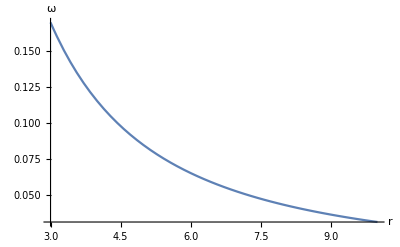

```mathematica
Plot[ω[r],{r,3,10},AxesLabel->{"r","ω"}]
```

#### Knowing the expression for epicyclic frequencies, plot them , a=0.7, where:

#### 1. For epicyclic frequency of Azimuthal component :

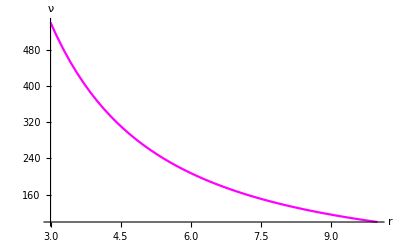

```mathematica
p1=Plot[ω[r]*(0.2035*10^4)/2π,{r,3,10},AxesLabel->{"r","ν"},PlotStyle->Magenta]
```

#### 2. For epicyclic frequency of Radial component :

```mathematica
a=0.7;
```

```mathematica
θ=π/2;
```

```mathematica
ω1[r_]=ω[r] √(1-6(r^-1)+8a(r^(-3/2))-3a^2(r^-2))
```

{(√(1-1.47/r^2+5.6/r^(3/2)-6/r) (-(2.8 r^2)/((0.+r^2)^2)+1.4/(0.+r^2)+√(((2.8 r^2)/((0.+r^2)^2)-1.4/(0.+r^2))^2-(2 r-(1.96 r^2)/((0.+r^2)^2)+0.98/(0.+r^2)) (-(4 r^2)/((0.+r^2)^2)+2/(0.+r^2)))))/(2 r-(1.96 r^2)/((0.+r^2)^2)+0.98/(0.+r^2))}
 |  |  |  |

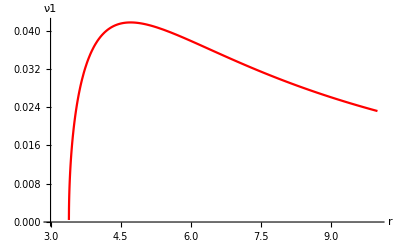

```mathematica
Plot[ω1[r],{r,3,10},AxesLabel->{"r","ν1"},PlotStyle->Red]
```

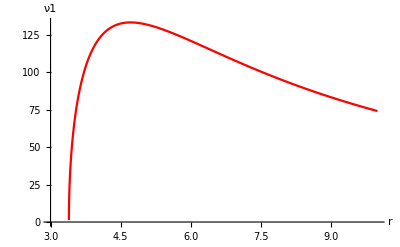

```mathematica
p2=Plot[ω1[r]*(0.2035*10^4)/2π,{r,3,10},AxesLabel->{"r","ν1"},PlotStyle->Red]
```

#### 3. For epicyclic frequency of vertical component :

```mathematica
a=0.7;
```

```mathematica
θ=π/2;
```

```mathematica
ω2[r_]=ω[r] √(1-4a(r^(-3/2))+3a^2(r^-2))
```

{(√(1+1.47/r^2-2.8/r^(3/2)) (-(2.8 r^2)/((0.+r^2)^2)+1.4/(0.+r^2)+√(((2.8 r^2)/((0.+r^2)^2)-1.4/(0.+r^2))^2-(2 r-(1.96 r^2)/((0.+r^2)^2)+0.98/(0.+r^2)) (-(4 r^2)/((0.+r^2)^2)+2/(0.+r^2)))))/(2 r-(1.96 r^2)/((0.+r^2)^2)+0.98/(0.+r^2))}
 |  |  |  |

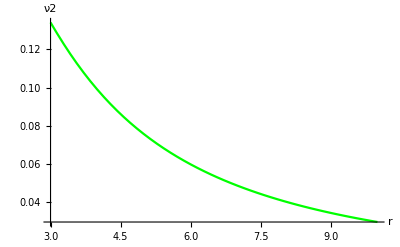

```mathematica
Plot[ω2[r],{r,3,10},AxesLabel->{"r","ν2"},PlotStyle->Green]
```

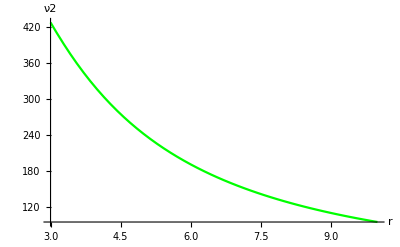

```mathematica
p3=Plot[ω2[r]*(0.2035*10^4)/2π,{r,3,10},AxesLabel->{"r","ν2"},PlotStyle->Green]
```

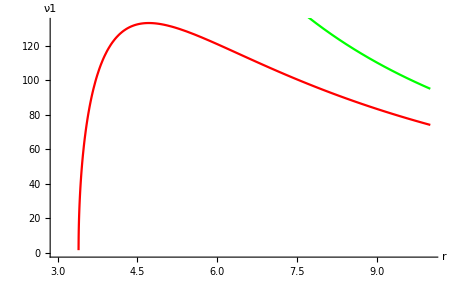

```mathematica
Show[p2,p3,AxesOrigin ->Automatic]
```

## For different values of “a”: Radial

### For a=0:

#### Geodesic equations for the equatorial plane :

```mathematica
Clear[k]
```

### 1. dt/dτ →dtdτ[r, Em, L]

```mathematica
a=0;
```

```mathematica
dtdτ [r_,Em_,L_]:=(1/Δ)[(r^2+a^2+(2a^2 r e^(-k/r)/ρ[r]))Em-(-2a r e^(-k/r)/ρ[r])L]
```

```mathematica
dtdτ [r,Em,L]
```

1/Δ[Em r^2]

### 2. dϕ/dτ →dϕdτ [r, L, Em]

```mathematica
a=0;
```

```mathematica
dϕdτ [r_,Em_,L_]:=(1/Δ)[(1-(2r e^(-k/r)/ρ[r]))L+(-2a r e^(-k/r)/ρ[r])Em]
```

```mathematica
dϕdτ [r,Em,L]
```

1/Δ[L (1-(2 e^(-k/r))/r)]
 |  |  |  |

### 3. dr/dτ →drdτ [r, L, Em]

```mathematica
a=0;
```

```mathematica
drdτ[r_,Em_,L_]:=√(rr[r]^-1)[-1-{Em^2(tt[r]×(dtdτ [r,Em,L])^2)}+{2L×Em×tϕ[r]×(dtdτ [r,Em,L])^2×(dϕdτ [r,Em,L])^2}-{L^2×ϕϕ[r]×(dϕdτ [r,Em,L])^2}]
```

```mathematica
drdτ [r,Em,L]
```

√((-2 e^(-k/r) r+r^2)/r^2[{{-1-L^2 (0.49+r^2+(0.98 e^(-k/r) r)/(0.+r^2)) (1/Δ[L (1-(2 e^(-k/r))/r)])^2-Em^2 (-1+(2 e^(-k/r) r)/(0.+r^2)) (1/Δ[Em r^2])^2-(2.8 e^(-k/r) Em L r (1/Δ[L (1-(2 e^(-k/r))/r)])^2 (1/Δ[Em r^2])^2)/(0.+r^2)}}])
 |  |  |  |

```mathematica
drdτ [r,Em,L]^2//Expand
```

(-2 e^(-k/r) r+r^2)/r^2[{{-1-L^2 (0.49+r^2+(0.98 e^(-k/r) r)/(0.+r^2)) (1/Δ[L (1-(2 e^(-k/r))/r)])^2-Em^2 (-1+(2 e^(-k/r) r)/(0.+r^2)) (1/Δ[Em r^2])^2-(2.8 e^(-k/r) Em L r (1/Δ[L (1-(2 e^(-k/r))/r)])^2 (1/Δ[Em r^2])^2)/(0.+r^2)}}]
 |  |  |  |

## For the epicyclic frequencies (ω):

```mathematica
a=0;
```

```mathematica
θ=π/2;
```

```mathematica
tt[r_]=-{1-2r e^(-k/r)/ρ[r]};
```

```mathematica
D[tt[r],r]//FullSimplify
```

{-(2 e^(-k/r) (r-k Log[e]))/r^3}
 |  |  |  |

```mathematica
tϕ[r_]=-2a r e^(-k/r)(Sin[θ])^2/ρ[r];
```

```mathematica
D[tϕ[r],r]//FullSimplify
```

0

```mathematica
ϕϕ[r_]=(r^2+a^2+(2a^2 r e^(-k/r)(Sin[θ])^2/ρ[r]))(Sin[θ])^2;
```

```mathematica
D[ϕϕ[r],r]//FullSimplify
```

2 r

## PLOTS:

### Knowing the expression for ω, plot “ν vs r” with a=0, where:

```mathematica
Clear[k]
```

```mathematica
k=0;
```

```mathematica
ω[r_]=(-D[tϕ[r],r]+√(D[tϕ[r],r]^2-D[tt[r],r]D[ϕϕ[r],r]))/D[ϕϕ[r],r]
```

{(1/r)^(3/2)}

#### For Figure 1 (Maselli 2017), Knowing the expression for epicyclic frequencies, plot them , a=0.7, where:

#### 1. For epicyclic frequency of Azimuthal component :

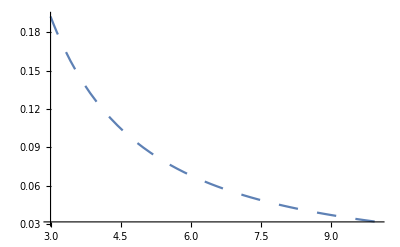

```mathematica
Plot[ω[r],{r,3,10},PlotStyle->{Dashing[Large]}]
```

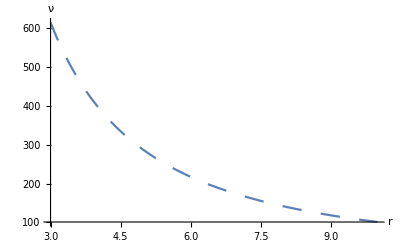

```mathematica
p4=Plot[ω[r]*(0.2035*10^4)/2π,{r,3,10},PlotStyle->{Dashing[Large]},AxesLabel->{"r","ν"}]
```

#### 2. For epicyclic frequency of Radial component :

```mathematica
a=0;
```

```mathematica
θ=π/2;
```

```mathematica
ω1[r_]=ω[r] √(1-6(r^-1)+8a(r^(-3/2))-3a^2(r^-2))
```

{√(1-6/r) (1/r)^(3/2)}
 |  |  |  |

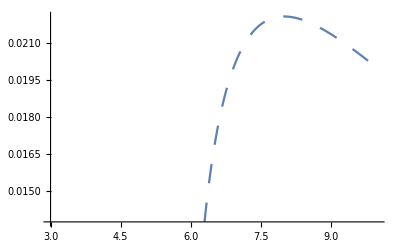

```mathematica
Plot[ω1[r],{r,3,10},PlotStyle->{Dashing[Large]}]
```

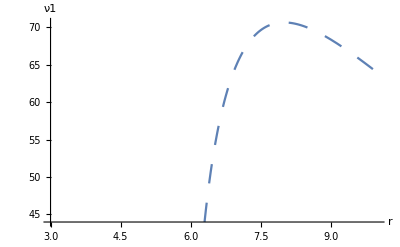

```mathematica
p5=Plot[ω1[r]*(0.2035*10^4)/2π,{r,3,10},PlotStyle->{Dashing[Large]},AxesLabel->{"r","ν1"}]
```

#### 3. For epicyclic frequency of vertical component :

```mathematica
a=0;
```

```mathematica
θ=π/2;
```

```mathematica
ω2[r_]=ω[r] √(1-4a(r^(-3/2))+3a^2(r^-2))
```

{(1/r)^(3/2)}

```mathematica
Plot[ω2[r],{r,3,10},PlotStyle->{Dashing[Large]}]
```

-Graphics-

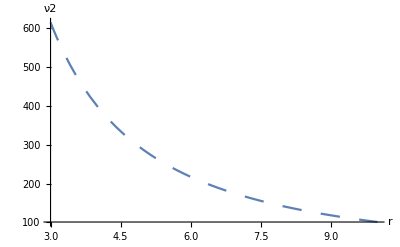

```mathematica
p6=Plot[ω2[r]*(0.2035*10^4)/2π,{r,3,10},AxesLabel->{"r","ν2"},PlotStyle->{Dashing[Large]}]
```

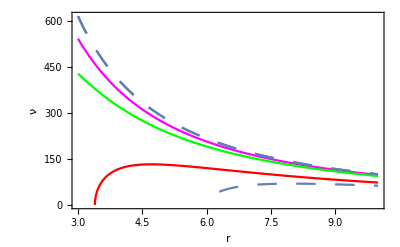

```mathematica
Show[p1,p2,p3,p4,p5,p6,PlotRange->All,Frame ->True,AxesOrigin ->Automatic]
```

```mathematica
Show[%88,FrameLabel->{{HoldForm[HoldForm["ν[Hz]"]],None},{HoldForm[HoldForm["r/M"]],None}},PlotLabel->HoldForm[EPICYCLIC FREQUENCIES]]
```